# p=3

## G_p

### data

```mathematica
p0=3.;
temperature={0.22, 0.2 ,0.18, 0.16 ,0.14 ,0.12, 0.1 ,0.09 ,0.08 ,0.075};
temperatures={0.22, 0.2 ,0.18, 0.16 ,0.14 ,0.12, 0.1 ,0.09 ,0.08 ,0.075};
tauEstimate={10 ,10, 10 ,50 ,100, 200 ,500, 2000 ,5000, 10000};
```

```mathematica
SACtime=
Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p","/SACtime_N4096_p","_T","_waitingTime","_idx",".nc"},{p0,p0,temperatures[[T]],If[tauEstimate[[T]]==999999,999999,If[tauEstimate[[T]]<100,1000,tauEstimate[[T]]*10]],rec},{3,4,8,0,0}],"Data"],{rec,0,9}],$Failed],{T,Length[temperatures]}];
```

### mean G

```mathematica
SACtimeMean=Table[Table[Mean[DeleteCases[Table[SACtime[[T,i,1,rec]],{i,Length[SACtime[[T]]]}],_Missing|_Part]],{rec,Max[Table[Length[SACtime[[T,i,1]]],{i,Length[SACtime[[T]]]}]]-3}],{T,Length[temperatures]}];
```

```mathematica
SACtimeVar=Table[Table[Variance[DeleteCases[Table[SACtime[[T,i,1,rec]],{i,Length[SACtime[[T]]]}],_Missing|_Part]],{rec,Max[Table[Length[SACtime[[T,i,1]]],{i,Length[SACtime[[T]]]}]]-3}],{T,Length[temperatures]}];
```

0.01

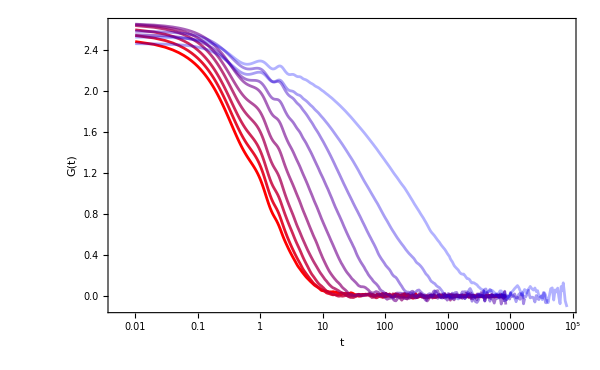

```mathematica
GtPlot=ListLogLinearPlot[Table[Table[{SACtime[[T,1,2,rec]],SACtimeMean[[T,rec]]*4096/temperatures[[T]]},{rec,Min[Length[SACtimeMean[[T]]],Length[SACtime[[T,1,2]]]]}],{T,1,Length[temperatures]}],PlotStyle->redBluePlotConfig[Length[temperatures]],FrameLabel->{"t","G(t) "},ImageSize->600,Joined->True,PlotRange->{All,All}]
```

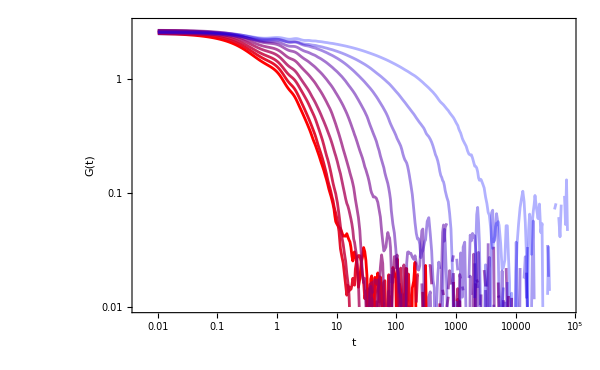

```mathematica
ListLogLogPlot[Table[Table[{SACtime[[T,1,2,rec]],SACtimeMean[[T,rec]]*4096/temperatures[[T]]},{rec,Min[Length[SACtimeMean[[T]]],Length[SACtime[[T,1,2]]]]}],{T,1,Length[temperatures]}],PlotStyle->redBluePlotConfig[Length[temperatures]],FrameLabel->{"t","G(t) "},ImageSize->600,Joined->True,PlotRange->{All,{0.01,3}}]
```

### fitting

```mathematica
fitStartPos=Table[{},{T,Length[temperature]}];
fitEndPos=Table[{},{T,Length[temperature]}];
betaConstraints=Table[{},{T,Length[temperature]}];
plateauConstraints=Table[{},{T,Length[temperature]}];
tauConstraints=Table[{},{T,Length[temperature]}];
fittings=Table[{},{T,Length[temperature]}];
initialPlateau=Table[{},{T,Length[temperature]}];
initialBeta=Table[{},{T,Length[temperature]}];
initialTau=Table[{},{T,Length[temperature]}];
```

```mathematica
betaResults=Table[{},{T,Length[temperature]}];
tauAlphaResults=Table[{},{T,Length[temperature]}];
plateauResults=Table[{},{T,Length[temperature]}];
```

```mathematica
numExp=Table[{},{T,Length[temperature]}];
```

```mathematica
noiseLevel=Table[{},{T,Length[temperature]}];
```

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

### fitting

#### T=0.075

```mathematica
Length[SACtime[[curT]]]
```

10

```mathematica
curT=10;
Table[ListLogLogPlot[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SACtime[[curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperature]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0=3.75 at T = "<>ToString[temperature[[curT]]],Joined->False,PlotRange->{All,All}],{i,Length[SACtime[[curT]]]}]
```

```mathematica
noiseLevel[[curT]]={0.5,0.5,0.71,0.85,0.82,0.62,0.61,0.54,1.07,0.86}
```

{0.5,0.5,0.71,0.85,0.82,0.62,0.61,0.54,1.07,0.86}

```mathematica
fitStartPos[[curT]]=Table[Position[Normal[SACtime[[curT,i,2]]],_?(#>2&)][[1,1]],{i,Length[SACtime[[curT]]]}]
```

{75,75,75,75,75,75,75,75,75,75}

```mathematica
fitEndPos[[curT]]=Table[Position[Normal[SACtime[[curT,i,1,fitStartPos[[curT,i]];;]]*4096/temperature[[curT]]],_?(# <noiseLevel[[curT,i]]&)][[1,1]]+fitStartPos[[curT,i]],{i,Length[SACtime[[curT]]]}]
```

{198,195,208,197,195,207,202,201,204,209}

```mathematica
initialPlateau[[curT]]=0.5;
initialBeta[[curT]]=0.75;
initialTau[[curT]]=100.;
betaConstraints[[curT]]={1.0>β>0.3,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curT]]={5.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curT]]=Table[NonlinearModelFit[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,fitStartPos[[curT,i]],fitEndPos[[curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curT,1]],plateauConstraints[[curT,1]],5000>τ>0.5}},{{G,initialPlateau[[curT]]},{τ,initialTau[[curT]]},{β,initialBeta[[curT]]}},t],{i,Length[SACtime[[curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]]]
```

{2.36255,2.06146,2.73444,2.34433,2.34411,2.64934,2.62123,2.48462,2.92672,2.30839}

2.480.25

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]]]
```

{196.143,180.716,299.386,337.829,303.467,263.904,201.355,165.675,574.641,595.891}

312.155.

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]]]
```

{0.556125,0.529405,0.44088,0.426014,0.405418,0.448036,0.468254,0.420001,0.47593,0.405473}

0.460.05

```mathematica
Table[Show[ListLogLogPlot[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SACtime[[curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperature]],Joined->True],LogLogPlot[fittings[[curT,i]][x],{x,SACtime[[curT,i,2,fitStartPos[[curT,i]]]],10000}]],{i,Length[SACtime[[curT]]]}]
```

#### T=0.08

```mathematica
curT=9;
Table[ListLogLogPlot[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SACtime[[curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperature]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0=3.75 at T = "<>ToString[temperature[[curT]]],Joined->False,PlotRange->{All,All}],{i,Length[SACtime[[curT]]]}]
```

```mathematica
noiseLevel[[curT]]={0.43,0.97,0.37,0.69,0.236,0.559,0.515,0.512,0.545,0.369}
```

{0.43,0.97,0.37,0.69,0.236,0.559,0.515,0.512,0.545,0.369}

```mathematica
fitStartPos[[curT]]=Table[Position[Normal[SACtime[[curT,i,2]]],_?(#>2&)][[1,1]],{i,Length[SACtime[[curT]]]}]
```

{75,75,75,75,75,75,75,75,75,75}

```mathematica
fitEndPos[[curT]]=Table[Position[Normal[SACtime[[curT,i,1,fitStartPos[[curT,i]];;]]*4096/temperature[[curT]]],_?(# <noiseLevel[[curT,i]]&)][[1,1]]+fitStartPos[[curT,i]],{i,Length[SACtime[[curT]]]}]
```

{188,164,182,181,195,167,177,172,183,191}

```mathematica
initialPlateau[[curT]]=0.5;
initialBeta[[curT]]=0.75;
initialTau[[curT]]=100.;
betaConstraints[[curT]]={1.0>β>0.3,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curT]]={5.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curT]]=Table[NonlinearModelFit[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,fitStartPos[[curT,i]],fitEndPos[[curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curT,1]],plateauConstraints[[curT,1]],5000>τ>0.5}},{{G,initialPlateau[[curT]]},{τ,initialTau[[curT]]},{β,initialBeta[[curT]]}},t],{i,Length[SACtime[[curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]]]
```

{2.46581,2.64871,2.28765,2.67453,2.2691,2.12781,2.34321,2.2355,2.5469,2.43837}

2.400.18

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]]]
```

{82.6788,87.6793,73.7293,105.265,52.8121,68.3003,70.1051,72.0126,94.4169,76.8115}

78.15.

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]]]
```

{0.482283,0.604865,0.599588,0.492565,0.483822,0.649789,0.54979,0.606694,0.52222,0.493526}

0.550.06

```mathematica
Table[Show[ListLogLogPlot[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SACtime[[curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperature]],Joined->True],LogLogPlot[fittings[[curT,i]][x],{x,SACtime[[curT,i,2,fitStartPos[[curT,i]]]],10000}]],{i,Length[SACtime[[curT]]]}]
```

#### T=0.09

```mathematica
curT=8;
Table[ListLogLogPlot[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SACtime[[curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperature]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0=3.75 at T = "<>ToString[temperature[[curT]]],Joined->False,PlotRange->{All,All}],{i,Length[SACtime[[curT]]]}]
```

```mathematica
noiseLevel[[curT]]={0.228,0.123,0.630,0.2,0.661,0.647,0.403,0.302,0.66,0.48}
```

{0.228,0.123,0.63,0.2,0.661,0.647,0.403,0.302,0.66,0.48}

```mathematica
fitStartPos[[curT]]=Table[Position[Normal[SACtime[[curT,i,2]]],_?(#>1&)][[1,1]],{i,Length[SACtime[[curT]]]}]
```

{59,59,59,59,59,59,59,59,59,59}

```mathematica
fitEndPos[[curT]]=Table[Position[Normal[SACtime[[curT,i,1,fitStartPos[[curT,i]];;]]*4096/temperature[[curT]]],_?(# <noiseLevel[[curT,i]]&)][[1,1]]+fitStartPos[[curT,i]],{i,Length[SACtime[[curT]]]}]
```

{166,169,161,164,151,148,151,165,151,160}

```mathematica
initialPlateau[[curT]]=0.5;
initialBeta[[curT]]=0.75;
initialTau[[curT]]=100.;
betaConstraints[[curT]]={1.0>β>0.3,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curT]]={5.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curT]]=Table[NonlinearModelFit[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,fitStartPos[[curT,i]],fitEndPos[[curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curT,1]],plateauConstraints[[curT,1]],5000>τ>0.5}},{{G,initialPlateau[[curT]]},{τ,initialTau[[curT]]},{β,initialBeta[[curT]]}},t],{i,Length[SACtime[[curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]]]
```

{2.36006,2.38305,2.79457,2.15185,2.59157,2.47746,2.18129,2.66886,2.44244,2.64249}

2.470.21

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]]]
```

{30.6653,29.8521,40.1854,29.3946,26.6558,30.6736,24.9229,33.4663,29.4338,33.5163}

31.4.

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]]]
```

{0.638659,0.706951,0.580151,0.731053,0.534846,0.698157,0.739325,0.678646,0.511401,0.597082}

0.640.08

```mathematica
Table[Show[ListLogLogPlot[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SACtime[[curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperature]],Joined->True],LogLogPlot[fittings[[curT,i]][x],{x,SACtime[[curT,i,2,fitStartPos[[curT,i]]]],10000}]],{i,Length[SACtime[[curT]]]}]
```

#### T=0.1

```mathematica
curT=7;
Table[ListLogLogPlot[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SACtime[[curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperature]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0=3.75 at T = "<>ToString[temperature[[curT]]],Joined->False,PlotRange->{All,All}],{i,Length[SACtime[[curT]]]}]
```

```mathematica
noiseLevel[[curT]]={0.14,0.27,0.12,0.16,0.103,0.146,0.336,0.254,0.135,0.216}
```

{0.14,0.27,0.12,0.16,0.103,0.146,0.336,0.254,0.135,0.216}

```mathematica
fitStartPos[[curT]]=Table[Position[Normal[SACtime[[curT,i,2]]],_?(#>1&)][[1,1]],{i,Length[SACtime[[curT]]]}]
```

{59,59,59,59,59,59,59,59,59,59}

```mathematica
fitEndPos[[curT]]=Table[Position[Normal[SACtime[[curT,i,1,fitStartPos[[curT,i]];;]]*4096/temperature[[curT]]],_?(# <noiseLevel[[curT,i]]&)][[1,1]]+fitStartPos[[curT,i]],{i,Length[SACtime[[curT]]]}]
```

{151,149,157,153,153,155,163,147,155,143}

```mathematica
initialPlateau[[curT]]=0.5;
initialBeta[[curT]]=0.75;
initialTau[[curT]]=100.;
betaConstraints[[curT]]={1.0>β>0.3,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curT]]={5.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curT]]=Table[NonlinearModelFit[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,fitStartPos[[curT,i]],fitEndPos[[curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curT,1]],plateauConstraints[[curT,1]],5000>τ>0.5}},{{G,initialPlateau[[curT]]},{τ,initialTau[[curT]]},{β,initialBeta[[curT]]}},t],{i,Length[SACtime[[curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]]]
```

{2.21845,2.32803,2.44042,2.44388,2.0759,2.3311,3.0871,2.36075,2.36908,2.19601}

2.390.27

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]]]
```

{13.7132,14.5488,15.38,17.8877,13.8574,16.8811,18.7882,15.3815,16.1834,15.444}

15.81.7

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]]]
```

{0.731599,0.668103,0.627203,0.80221,0.819885,0.754664,0.522034,0.70279,0.712458,0.81164}

0.720.09

#### T=0.14

```mathematica
curT=5;
Table[ListLogLogPlot[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SACtime[[curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperature]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0=3.75 at T = "<>ToString[temperature[[curT]]],Joined->False,PlotRange->{All,All}],{i,Length[SACtime[[curT]]]}]
```

```mathematica
noiseLevel[[curT]]={0.088,0.182,0.071,0.141,0.182,0.103,0.101,0.264,0.088,0.264}
```

{0.088,0.182,0.071,0.141,0.182,0.103,0.101,0.264,0.088,0.264}

```mathematica
fitStartPos[[curT]]=Table[Position[Normal[SACtime[[curT,i,2]]],_?(#>2&)][[1,1]],{i,Length[SACtime[[curT]]]}]
```

{75,75,75,75,75,75,75,75,75,75}

```mathematica
fitEndPos[[curT]]=Table[Position[Normal[SACtime[[curT,i,1,fitStartPos[[curT,i]];;]]*4096/temperature[[curT]]],_?(# <noiseLevel[[curT,i]]&)][[1,1]]+fitStartPos[[curT,i]],{i,Length[SACtime[[curT]]]}]
```

{130,121,125,122,120,130,134,116,131,117}

```mathematica
initialPlateau[[curT]]=0.5;
initialBeta[[curT]]=0.75;
initialTau[[curT]]=100.;
betaConstraints[[curT]]={1.0>β>0.3,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curT]]={5.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curT]]=Table[NonlinearModelFit[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,fitStartPos[[curT,i]],fitEndPos[[curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curT,1]],plateauConstraints[[curT,1]],5000>τ>0.5}},{{G,initialPlateau[[curT]]},{τ,initialTau[[curT]]},{β,initialBeta[[curT]]}},t],{i,Length[SACtime[[curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]]]
```

{2.45634,2.26685,1.93659,2.17925,2.33047,2.5118,3.8383,2.50107,2.22607,2.37836}

2.50.5

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]]]
```

{4.67744,4.85376,5.77855,5.55271,4.60483,4.62168,1.81334,3.75587,5.19638,4.80538}

4.61.1

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]]]
```

{0.770598,0.808455,0.999996,0.906151,0.791261,0.78895,0.501873,0.725182,0.795447,0.840659}

0.790.13

```mathematica
Table[Show[ListLogLogPlot[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SACtime[[curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperature]],Joined->True],LogLogPlot[fittings[[curT,i]][x],{x,SACtime[[curT,i,2,fitStartPos[[curT,i]]]],10000}]],{i,Length[SACtime[[curT]]]}]
```

#### T=0.12

```mathematica
curT=6;
Table[ListLogLogPlot[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SACtime[[curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperature]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0=3.75 at T = "<>ToString[temperature[[curT]]],Joined->False,PlotRange->{All,All}],{i,Length[SACtime[[curT]]]}]
```

```mathematica
noiseLevel[[curT]]={0.309,0.268,0.1,0.12,0.166,0.110,0.0508,0.0653,0.212,0.3}
```

{0.309,0.268,0.1,0.12,0.166,0.11,0.0508,0.0653,0.212,0.3}

```mathematica
fitStartPos[[curT]]=Table[Position[Normal[SACtime[[curT,i,2]]],_?(#>2&)][[1,1]],{i,Length[SACtime[[curT]]]}]
```

{75,75,75,75,75,75,75,75,75,75}

```mathematica
fitEndPos[[curT]]=Table[Position[Normal[SACtime[[curT,i,1,fitStartPos[[curT,i]];;]]*4096/temperature[[curT]]],_?(# <noiseLevel[[curT,i]]&)][[1,1]]+fitStartPos[[curT,i]],{i,Length[SACtime[[curT]]]}]
```

{128,133,136,136,141,143,138,147,134,135}

```mathematica
initialPlateau[[curT]]=0.5;
initialBeta[[curT]]=0.75;
initialTau[[curT]]=100.;
betaConstraints[[curT]]={1.0>β>0.3,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curT]]={5.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curT]]=Table[NonlinearModelFit[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,fitStartPos[[curT,i]],fitEndPos[[curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curT,1]],plateauConstraints[[curT,1]],5000>τ>0.5}},{{G,initialPlateau[[curT]]},{τ,initialTau[[curT]]},{β,initialBeta[[curT]]}},t],{i,Length[SACtime[[curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]]]
```

{2.41236,2.61441,2.03691,2.23156,2.44724,2.76667,2.16536,2.43936,2.50841,3.04194}

2.470.29

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]]]
```

{7.77922,7.24288,9.01801,7.3505,8.37165,7.07754,7.90493,8.24673,7.56927,5.48491}

7.60.9

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]]]
```

{0.764902,0.669705,0.900895,0.777692,0.736761,0.670589,0.899649,0.690662,0.750522,0.538206}

0.740.11

```mathematica
Table[Show[ListLogLogPlot[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SACtime[[curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperature]],Joined->True],LogLogPlot[fittings[[curT,i]][x],{x,SACtime[[curT,i,2,fitStartPos[[curT,i]]]],10000}]],{i,Length[SACtime[[curT]]]}]
```

#### T=0.16

```mathematica
curT=4;
Table[ListLogLogPlot[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SACtime[[curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperature]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0=3.75 at T = "<>ToString[temperature[[curT]]],Joined->False,PlotRange->{All,All}],{i,Length[SACtime[[curT]]]}]
```

```mathematica
noiseLevel[[curT]]={0.0136,0.124,0.0389,0.0613,0.078,0.108,0.0911,0.0734,0.0269,0.210}
```

{0.0136,0.124,0.0389,0.0613,0.078,0.108,0.0911,0.0734,0.0269,0.21}

```mathematica
fitStartPos[[curT]]=Table[Position[Normal[SACtime[[curT,i,2]]],_?(#>1.5&)][[1,1]],{i,Length[SACtime[[curT]]]}]
```

{68,68,68,68,68,68,68,68,68,68}

```mathematica
fitEndPos[[curT]]=Table[Position[Normal[SACtime[[curT,i,1,fitStartPos[[curT,i]];;]]*4096/temperature[[curT]]],_?(# <noiseLevel[[curT,i]]&)][[1,1]]+fitStartPos[[curT,i]],{i,Length[SACtime[[curT]]]}]
```

{123,117,120,119,120,124,121,121,132,111}

```mathematica
initialPlateau[[curT]]=0.5;
initialBeta[[curT]]=0.75;
initialTau[[curT]]=100.;
betaConstraints[[curT]]={1.0>β>0.3,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curT]]={5.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curT]]=Table[NonlinearModelFit[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,fitStartPos[[curT,i]],fitEndPos[[curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curT,1]],plateauConstraints[[curT,1]],5000>τ>0.5}},{{G,initialPlateau[[curT]]},{τ,initialTau[[curT]]},{β,initialBeta[[curT]]}},t],{i,Length[SACtime[[curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]]]
```

{2.44824,2.42705,2.10447,2.19781,2.59316,2.61175,3.36085,2.18747,2.94176,2.4373}

2.50.4

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]]]
```

{2.44587,2.81668,3.43361,3.33431,2.69623,2.88276,1.79419,3.49318,2.31221,2.84664}

2.80.5

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]]]
```

{0.712951,0.765937,0.947773,0.848652,0.71527,0.676177,0.592508,0.841439,0.661922,0.796303}

0.760.11

```mathematica
Table[Show[ListLogLogPlot[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SACtime[[curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperature]],Joined->True],LogLogPlot[fittings[[curT,i]][x],{x,SACtime[[curT,i,2,fitStartPos[[curT,i]]]],10000}]],{i,Length[SACtime[[curT]]]}]
```

#### T=0.18

```mathematica
curT=3;
Table[ListLogLogPlot[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SACtime[[curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperature]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0=3.75 at T = "<>ToString[temperature[[curT]]],Joined->False,PlotRange->{All,All}],{i,Length[SACtime[[curT]]]}]
```

```mathematica
noiseLevel[[curT]]={0.131,0.106,0.0607,0.0899,0.0345,0.102,0.0208,0.0963,0.0685,0.107}
```

{0.131,0.106,0.0607,0.0899,0.0345,0.102,0.0208,0.0963,0.0685,0.107}

```mathematica
fitStartPos[[curT]]=Table[Position[Normal[SACtime[[curT,i,2]]],_?(#>1.5&)][[1,1]],{i,Length[SACtime[[curT]]]}]
```

{68,68,68,68,68,68,68,68,68,68}

```mathematica
fitEndPos[[curT]]=Table[Position[Normal[SACtime[[curT,i,1,fitStartPos[[curT,i]];;]]*4096/temperature[[curT]]],_?(# <noiseLevel[[curT,i]]&)][[1,1]]+fitStartPos[[curT,i]],{i,Length[SACtime[[curT]]]}]
```

{108,108,115,113,122,115,118,107,114,108}

```mathematica
initialPlateau[[curT]]=0.5;
initialBeta[[curT]]=0.75;
initialTau[[curT]]=100.;
betaConstraints[[curT]]={1.0>β>0.3,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curT]]={5.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curT]]=Table[NonlinearModelFit[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,fitStartPos[[curT,i]],fitEndPos[[curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curT,1]],plateauConstraints[[curT,1]],5000>τ>0.5}},{{G,initialPlateau[[curT]]},{τ,initialTau[[curT]]},{β,initialBeta[[curT]]}},t],{i,Length[SACtime[[curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]]]
```

{2.11502,2.34804,1.81788,2.15443,1.87215,1.88846,1.77378,1.85974,2.13637,1.99915}

2.000.19

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]]]
```

{2.71225,2.09597,3.01057,2.47007,3.31821,3.3959,2.96817,2.76339,2.53998,2.72902}

2.80.4

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]]]
```

{0.968603,0.786764,0.999989,0.832826,0.858771,0.942751,0.999983,0.999991,0.831028,0.955248}

0.920.08

```mathematica
Table[Show[ListLogLogPlot[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SACtime[[curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperature]],Joined->True],LogLogPlot[fittings[[curT,i]][x],{x,SACtime[[curT,i,2,fitStartPos[[curT,i]]]],10000}]],{i,Length[SACtime[[curT]]]}]
```

#### T=0.2

```mathematica
curT=2;
Table[ListLogLogPlot[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SACtime[[curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperature]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0=3.75 at T = "<>ToString[temperature[[curT]]],Joined->False,PlotRange->{All,All}],{i,Length[SACtime[[curT]]]}]
```

```mathematica
noiseLevel[[curT]]={0.0146,0.148,0.0486,0.0443,0.0772,0.0117,0.116,0.0862,0.111,0.163}
```

{0.0146,0.148,0.0486,0.0443,0.0772,0.0117,0.116,0.0862,0.111,0.163}

```mathematica
fitStartPos[[curT]]=Table[Position[Normal[SACtime[[curT,i,2]]],_?(#>1&)][[1,1]],{i,Length[SACtime[[curT]]]}]
```

{59,59,59,59,59,59,59,59,59,59}

```mathematica
fitEndPos[[curT]]=Table[Position[Normal[SACtime[[curT,i,1,fitStartPos[[curT,i]];;]]*4096/temperature[[curT]]],_?(# <noiseLevel[[curT,i]]&)][[1,1]]+fitStartPos[[curT,i]],{i,Length[SACtime[[curT]]]}]
```

{111,104,112,110,121,181,105,103,106,103}

```mathematica
initialPlateau[[curT]]=0.5;
initialBeta[[curT]]=0.75;
initialTau[[curT]]=100.;
betaConstraints[[curT]]={1.0>β>0.9999,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curT]]={5.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curT]]=Table[NonlinearModelFit[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,fitStartPos[[curT,i]],fitEndPos[[curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curT,1]],plateauConstraints[[curT,1]],5000>τ>0.5}},{{G,initialPlateau[[curT]]},{τ,initialTau[[curT]]},{β,initialBeta[[curT]]}},t],{i,Length[SACtime[[curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]]]
```

{1.83463,1.85728,1.77129,1.92058,1.53309,1.65188,1.91358,2.01614,1.86938,1.91135}

1.830.14

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]]]
```

{2.36012,2.53733,2.38318,2.08649,3.33382,3.08385,2.40403,2.0677,2.35345,2.31453}

2.50.4

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]]]
```

{0.99994,0.999902,0.9999,0.999901,0.9999,0.9999,0.999901,0.999934,0.9999,0.99993}

0.9999110.000017

```mathematica
Table[Show[ListLogLogPlot[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SACtime[[curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperature]],Joined->True],LogLogPlot[fittings[[curT,i]][x],{x,SACtime[[curT,i,2,fitStartPos[[curT,i]]]],10000}]],{i,Length[SACtime[[curT]]]}]
```

#### T=0.22

```mathematica
curT=1;
Table[ListLogLogPlot[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SACtime[[curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperature]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0=3.75 at T = "<>ToString[temperature[[curT]]],Joined->False,PlotRange->{All,All}],{i,Length[SACtime[[curT]]]}]
```

```mathematica
noiseLevel[[curT]]={0.0378,0.0282,0.0729,0.177,0.179,0.0417,0.0308,0.0181,0.266,0.127}
```

{0.0378,0.0282,0.0729,0.177,0.179,0.0417,0.0308,0.0181,0.266,0.127}

```mathematica
fitStartPos[[curT]]=Table[Position[Normal[SACtime[[curT,i,2]]],_?(#>1&)][[1,1]],{i,Length[SACtime[[curT]]]}]
```

{59,59,59,59,59,59,59,59,59,59}

```mathematica
fitEndPos[[curT]]=Table[Position[Normal[SACtime[[curT,i,1,fitStartPos[[curT,i]];;]]*4096/temperature[[curT]]],_?(# <noiseLevel[[curT,i]]&)][[1,1]]+fitStartPos[[curT,i]],{i,Length[SACtime[[curT]]]}]
```

{103,106,107,104,98,108,114,114,112,100}

```mathematica
initialPlateau[[curT]]=0.5;
initialBeta[[curT]]=0.75;
initialTau[[curT]]=100.;
betaConstraints[[curT]]={1.0>β>0.9999,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curT]]={5.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curT]]=Table[NonlinearModelFit[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,fitStartPos[[curT,i]],fitEndPos[[curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curT,1]],plateauConstraints[[curT,1]],5000>τ>0.5}},{{G,initialPlateau[[curT]]},{τ,initialTau[[curT]]},{β,initialBeta[[curT]]}},t],{i,Length[SACtime[[curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[curT]]]}]]]
```

{1.78957,1.89421,1.67093,1.49964,1.72598,1.8146,1.58141,1.81334,1.28117,1.75198}

1.680.18

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[curT]]]}]]]
```

{1.97457,1.86756,2.39776,2.67797,2.07987,2.00934,2.48258,2.06722,4.59008,1.97781}

2.40.8

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[curT]]]}]]]
```

{0.999943,0.999923,0.999902,0.9999,0.999922,0.999901,0.9999,0.999901,0.9999,0.999922}

0.9999110.000015

```mathematica
Table[Show[ListLogLogPlot[Table[{SACtime[[curT,i,2,rec]],SACtime[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SACtime[[curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperature]],Joined->True],LogLogPlot[fittings[[curT,i]][x],{x,SACtime[[curT,i,2,fitStartPos[[curT,i]]]],10000}]],{i,Length[SACtime[[curT]]]}]
```

#### general fittings

```mathematica
fittings
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
fittings={{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}};
```

### results

```mathematica
tauSResults=Table[Around[Mean[Table[fittings[[T,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[T]]]}]],StandardDeviation[Table[fittings[[T,i]]["BestFitParameters"][[2,2]],{i,Length[SACtime[[T]]]}]]],{T,Length[temperature]}]
plateauResults=Table[Around[Mean[Table[fittings[[T,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[T]]]}]],StandardDeviation[Table[fittings[[T,i]]["BestFitParameters"][[1,2]],{i,Length[SACtime[[T]]]}]]],{T,Length[temperature]}]
betaResults=Join[Table[Around[Mean[Table[fittings[[T,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[T]]]}]],StandardDeviation[Table[fittings[[T,i]]["BestFitParameters"][[3,2]],{i,Length[SACtime[[T]]]}]]],{T,Length[temperature]}]]
```

{2.40.8,2.50.4,2.80.4,2.80.5,4.61.1,7.60.9,15.81.7,31.4.,78.15.,312.155.}

{1.680.18,1.830.14,2.000.19,2.50.4,2.50.5,2.470.29,2.390.27,2.470.21,2.400.18,2.480.25}

{0.9999110.000015,0.9999110.000017,0.920.08,0.760.11,0.790.13,0.740.11,0.720.09,0.640.08,0.550.06,0.460.05}

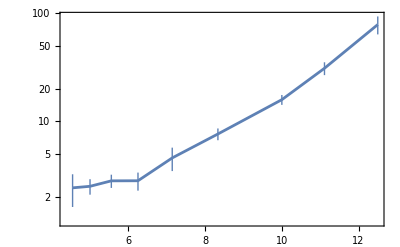

```mathematica
Show[ListLogPlot[Table[{1/temperature[[T]],tauSResults[[T]]},{T,Length[temperature]-1}],Joined->True]]
```

```mathematica
ListLogPlot[Table[{plateauResults[[T]]/temperature[[T]]^1.2,tauAlpha[[T]]},{T,Length[temperature]}],Joined->True,Ticks->None]
```

Part::partw: Part 4 of … does not exist.

Part::partw: Part 5 of … does not exist.

Part::partw: Part 6 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

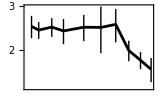

```mathematica
gp3=Show[ListLogLogPlot[Table[{temperature[[T]],plateauResults[[T]]},{T,Length[temperature]}],FrameTicks->{{{{1.5,1.5,0.04},{1.6,None,0.02},{1.7,None,0.02},{1.8,None,0.02},{1.9,None,0.02},{2,2,0.04},{2.1,None,0.02},{2.2,None,0.02},{2.3,None,0.02},{2.4,None,0.02},{2.5,2.5,0.04},{2.6,None,0.02},{2.7,None,0.02},{2.8,None,0.02},{2.9,None,0.02},{3,3,0.04}},None},{{{0.06,None,0.03},{0.07,None,0.03},{0.08,None,0.03},{0.09,None,0.03},{0.1,None,0.07},{0.11,None,0.03},{0.12,None,0.03},{0.13,None,0.03},{0.14,None,0.03},{0.15,None,0.03},{0.16,None,0.03},{0.17,None,0.03},{0.18,None,0.03},{0.19,None,0.03},{0.2,None,0.07}},None}},Joined->True,ImageSize->160,LabelStyle->Directive[FontSize->20],PlotStyle->Black]]
```

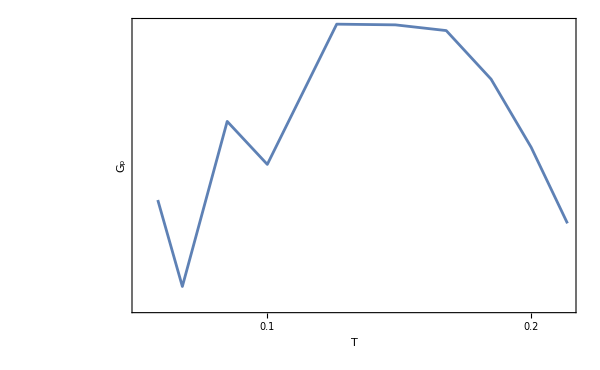

```mathematica
Show[ListLogLogPlot[Table[{temperature[[T]],SACtimeMean[[T,1]]*4096/temperatures[[T]]},{T,Length[temperature]}],Joined->True,ImageSize->600,LabelStyle->Directive[FontSize->20],FrameLabel->{"T","G_p"}],LogLogPlot[5*x^(-0.5),{x,0.001,0.7},PlotStyle->{Dashed,Red}]]
```

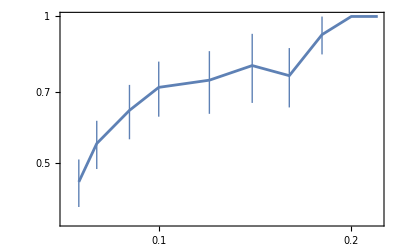

```mathematica
ListLogLogPlot[Table[{temperature[[T]],betaResults[[T]]},{T,Length[temperature]}],Joined->True]
```

## tau_alpha

### data

```mathematica
p0=3.;
temperature={0.22, 0.2 ,0.18, 0.16 ,0.14 ,0.12, 0.1 ,0.09 ,0.08 ,0.075};
temperature={0.22, 0.2 ,0.18, 0.16 ,0.14 ,0.12, 0.1 ,0.09 ,0.08 ,0.075};
tauEstimate={10 ,10, 10 ,50 ,100, 200 ,500, 2000 ,5000, 10000};
```

```mathematica
CRSISF=
Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/timeCRSISF_N4096_p","_T","_waitingTime","_idx",".nc"},{p0,p0,temperatures[[T]],If[tauEstimate[[T]]==999999,999999,If[tauEstimate[[T]]<100,1000,tauEstimate[[T]]*10]],rec},{3,4,8,0,0}],"Data"],{rec,0,9}],$Failed],{T,Length[temperatures]}];
```

```mathematica
CRoverlap=
Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/timeCRoverlap_N4096_p","_T","_waitingTime","_idx",".nc"},{p0,p0,temperatures[[T]],If[tauEstimate[[T]]==999999,999999,If[tauEstimate[[T]]<100,1000,tauEstimate[[T]]*10]],rec},{3,4,8,0,0}],"Data"],{rec,0,9}],$Failed],{T,Length[temperatures]}];
```

```mathematica
Normal[CRSISF[[1,1,2]]]
```

### mean CRSISF

```mathematica
CRSISFMean=Table[Table[Mean[DeleteCases[Table[CRSISF[[T,i,2,rec]],{i,Length[CRSISF[[T]]]}],_Missing|_Part]],{rec,Max[Table[Length[CRSISF[[T,i,1]]],{i,Length[CRSISF[[T]]]}]]-3}],{T,Length[temperatures]}];
```

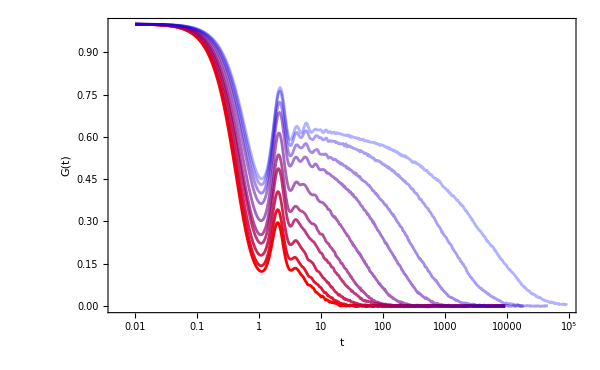

```mathematica
ListLogLinearPlot[Table[Table[{CRSISF[[T,1,1,rec]]-CRSISF[[T,1,1,1]],CRSISFMean[[T,rec]]},{rec,Min[Length[CRSISFMean[[T]]],Length[CRSISF[[T,1,2]]]]}],{T,1,Length[temperatures]}],PlotStyle->redBluePlotConfig[Length[temperatures]],FrameLabel->{"t","G(t) "},ImageSize->600,Joined->True,PlotRange->{All,All}]
```

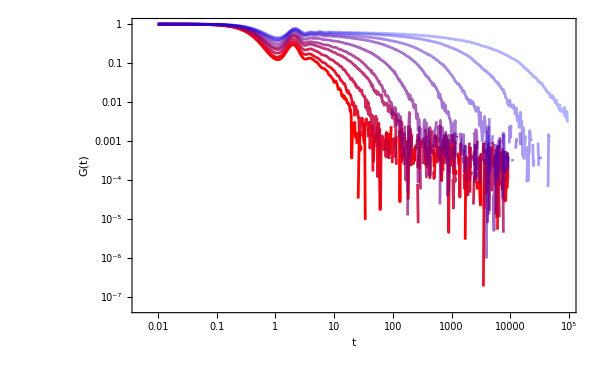

```mathematica
ListLogLogPlot[Table[Table[{CRSISF[[T,1,1,rec]]-CRSISF[[T,1,1,1]],CRSISFMean[[T,rec]]},{rec,Min[Length[CRSISFMean[[T]]],Length[CRSISF[[T,1,2]]]]}],{T,1,Length[temperatures]}],PlotStyle->redBluePlotConfig[Length[temperatures]],FrameLabel->{"t","G(t) "},ImageSize->600,Joined->True,PlotRange->{All,All}]
```

#### fit

```mathematica
absTime=Normal[CRSISF[[10,1,1]]]-CRSISF[[10,1,1,1]];
```

```mathematica
fitStartNumCRSISF={5,5,5,5,5,10,10,12,17,17};
```

```mathematica
fitEngNumCRSISF=0.001;
```

```mathematica
fitStartPosCRSISF=Table[Position[absTime,_?(#>fitStartNumCRSISF[[i]]&)][[1,1]],{i,Length[fitStartNumCRSISF]}]
```

{151,151,151,151,151,182,182,189,205,205}

```mathematica
fitEndPosCRSISF=Table[If[AllTrue[CRSISFMean[[i]],#>0&],Length[CRSISFMean[[i]]],Position[CRSISFMean[[i]],_?(#<fitEngNumCRSISF&)][[1,1]]-1],{i,Length[temperatures]}]
```

{210,233,250,291,297,328,380,432,501,578}

```mathematica
fitsCRSISF=Table[NonlinearModelFit[Table[{Normal[absTime[[rec]]],Normal[CRSISFMean[[T,rec]]]},{rec,fitStartPosCRSISF[[T]],fitEndPosCRSISF[[T]]}],{stretchedExp[t,G,τ,β],{1.0>G>0.4,1.0>β>0.2,50000>τ>0.5}},{{G},{τ},{β}},t],{T,Length[temperatures]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

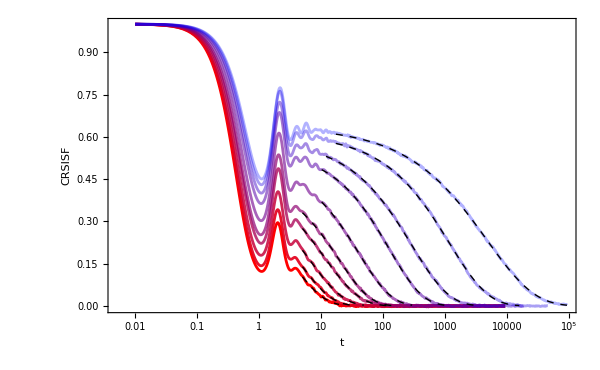

```mathematica
CRSISFPlot=Show[ListLogLinearPlot[Table[Table[{CRSISF[[T,1,1,rec]]-CRSISF[[T,1,1,1]],CRSISFMean[[T,rec]]},{rec,Min[Length[CRSISFMean[[T]]],Length[CRSISF[[T,1,2]]]]}],{T,1,Length[temperatures]}],PlotStyle->redBluePlotConfig[Length[temperatures]],FrameLabel->{"t","CRSISF "},ImageSize->600,Joined->True,PlotRange->{All,All}],Table[LogLinearPlot[fitsCRSISF[[T]][x],{x,absTime[[fitStartPosCRSISF[[T]]]],absTime[[fitEndPosCRSISF[[T]]]]},PlotStyle->{Dashed,Thick,Black}],{T,Length[temperatures]}]]
```

```mathematica
tauAlpha=Table[fitsCRSISF[[T]]["BestFitParameters"][[2,2]],{T,Length[temperature]}]
```

{3.44884,4.71076,6.77467,11.1304,19.3829,40.9127,125.394,291.209,1169.95,4772.3}

```mathematica
Table[fitsCRSISF[[T]]["BestFitParameters"][[1,2]],{T,Length[temperature]}]
```

{0.407125,0.400133,0.433039,0.476246,0.450548,0.507604,0.553011,0.587107,0.609624,0.635398}

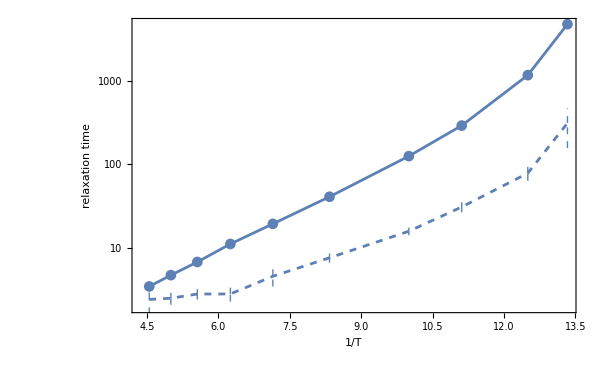

```mathematica
relaxationTimeFPlot=Show[ListLogPlot[Table[{1/temperature[[T]],tauAlpha[[T]]},{T,Length[temperature]}],Joined->True,PlotMarkers->Automatic,FrameLabel->{"1/T","relaxation time"}],ListLogPlot[Table[{1/temperature[[T]],tauSResults[[T]]},{T,Length[temperature]}],Joined->True,PlotStyle->Dashed],ImageSize->600]
```

```mathematica
Export["/home/chengling/Research/updates/09182024/CRSISF.jpeg",Grid[Partition[{CRSISFPlot,relaxationTimeFPlot},1]],ImageResolution->300]
```

/home/chengling/Research/updates/09182024/CRSISF.jpeg

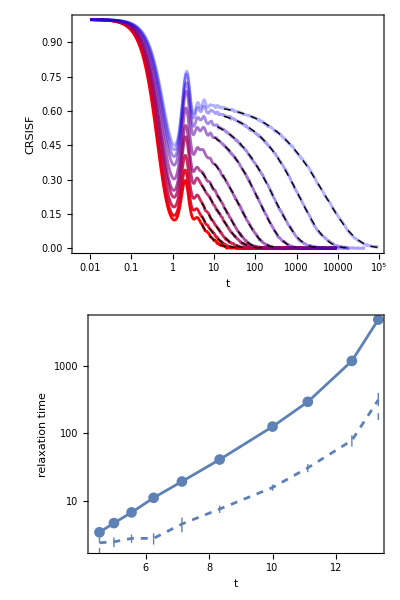

```mathematica
Grid[Partition[{CRSISFPlot,relaxationTimeFPlot},1]]
```

```mathematica
Export["/home/chengling/Research/updates/09182024/gp.jpeg",gp3,ImageResolution->300]
```

/home/chengling/Research/updates/09182024/gp.jpeg

```mathematica
Export["/home/chengling/Research/updates/09182024/gp.jpeg",Grid[Partition[{GtPlot,gp3},1]],ImageResolution->300]
```

/home/chengling/Research/updates/09182024/gp.jpeg

## Sq

### data

```mathematica
p0=3.;
temperature={0.22, 0.2 ,0.18, 0.16 ,0.14 ,0.12, 0.1 ,0.09 ,0.08 ,0.075};
temperatures={0.22, 0.2 ,0.18, 0.16 ,0.14 ,0.12, 0.1 ,0.09 ,0.08 ,0.075};
tauEstimate={10 ,10, 10 ,50 ,100, 200 ,500, 2000 ,5000, 10000};
```

```mathematica
sks=
Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p","/scatteringFunction_N4096_p","_T","_idx",".nc"},{p0,p0,temperatures[[T]],rec},{3,4,8,0,0}],"Data"],{rec,0,9}],$Failed],{T,Length[temperatures]}];
```

```mathematica
Normal[sks[[9,1,3]]]
```

{{50724.4},{50741.3},{50758.6},{50776.3},{50794.3},{50812.8},{50831.8},{50851.1},{50871.},{50891.3},{50912.},{50933.3},{50955.},{50977.2},{51000.},{51023.3},{51047.1},{51071.5},{51096.5},{51122.},{51148.2},{51174.9},{51202.3},{51230.3},{51258.9},{51288.3},{51318.3},{51349.},{51380.4},{51412.5},{51445.4},{51479.1},{51513.6},{51548.8},{51584.9},{51621.8},{51659.6},{51698.2},{51737.8},{51778.3},{51819.7},{51862.1},{51905.5},{51949.8},{51995.3},{52041.7},{52089.3},{52138.},{52187.8},{52238.7},{52290.9},{52344.2},{52398.8},{52454.7},{52511.9},{52570.4},{52630.3},{52691.5},{52754.2},{52818.4},{52884.},{52951.2},{53020.},{53090.3},{53162.3},{53235.9},{53311.3},{53388.4},{53467.4},{53548.1},{53630.8},{53715.4},{53801.9},{53890.5},{53981.1},{54073.8},{54168.7},{54265.8},{54365.2},{54466.8},{54570.9},{54677.4},{54786.3},{54897.8},{55011.9},{55128.6},{55248.1},{55370.3},{55495.4},{55623.4},{55754.4},{55888.4},{56025.6},{56166.},{56309.6},{56456.5},{56606.9},{56760.8},{56918.3},{57079.5},{57244.4},{57413.1},{57585.8},{57762.5},{57943.3},{58128.3},{58317.6},{58511.4},{58709.6},{58912.5},{59120.1},{59332.5},{59549.9},{59772.4},{60000.},{60232.9},{60471.3},{60715.2},{60964.8},{61220.2},{61481.5},{61749.},{62022.6},{62302.7},{62589.3},{62882.5},{63182.6},{63489.6},{63803.8},{64125.4},{64454.4},{64791.1},{65135.6},{65488.2},{65848.9},{66218.1},{66595.9},{66982.4},{67378.},{67782.8},{68197.},{68620.9},{69054.6},{69498.5},{69952.6},{70417.4},{70893.},{71379.6},{71877.6},{72387.2},{72908.7},{73442.3},{73988.3},{74547.1},{75118.9},{75704.},{76302.7},{76915.3},{77542.3},{78183.8},{78840.3},{79512.1},{80199.5},{80902.9},{81622.8},{82359.4},{83113.1},{83884.4},{84673.7},{85481.3},{86307.8},{87153.5},{88018.9},{88904.5},{89810.7},{90738.},{91686.9},{92657.9},{93651.6},{94668.4},{95708.8},{96773.5},{97863.},{98977.9}}

```mathematica
sksMean=Table[Table[Mean[Flatten[Table[Table[sks[[T,i,2,time,k]],{time,1,Length[sks[[T,i,2]]],30}],{i,Length[records]}]]],{k,Length[sks[[T,1,1,1]]]}],{T,Length[temperatures]}];
```

```mathematica
sksVar=Table[Table[Variance[Flatten[Table[Table[sks[[T,i,2,time,k]],{time,Length[sks[[T,i,2]]]}],{i,Length[records]}]]],{k,Length[sks[[T,1,1,1]]]}],{T,Length[temperatures]}];
```

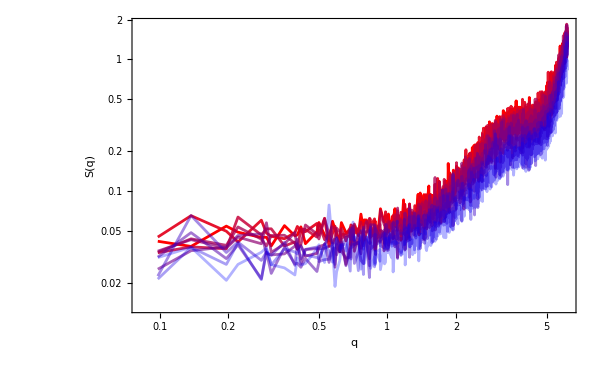

```mathematica
sqPLot=ListLogLogPlot[Table[Table[{sks[[T,1,1,1,rec]],sksMean[[T,rec]]},{rec,Length[sksMean[[T]]]}],{T,Length[temperatures]}],PlotStyle->redBluePlotConfig[Length[temperatures]],Joined->True,FrameLabel->{"q","S(q)"},ImageSize->600]
```

```mathematica
sks[[10,1,2,1]]
```

NumericArray[…]

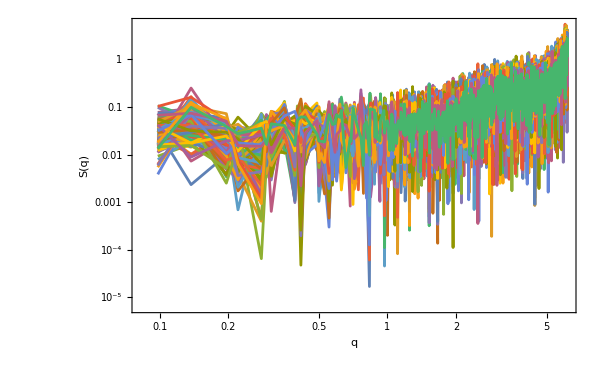

```mathematica
sqPLot=ListLogLogPlot[Table[Table[{sks[[8,1,1,1,rec]],sks[[8,1,2,time,rec]]},{rec,Length[sksMean[[8]]]}],{time,150}],Joined->True,FrameLabel->{"q","S(q)"},ImageSize->600]
```